```mathematica
SetDirectory[NotebookDirectory[]];
Remove["Global`*"]//Quiet;
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"lib_v_1.nb"}],InsertResults->False];
```

# Teoria gier

## Równowaga Nasha w terminach odwzorowania najlepszej odpowiedzi

### Definicja w terminach najlepszej odpowiedzi

Definicja. Niech dana będzie gra G=(ℐ,S,u). Przez odwzorowanie najlepszej odpowiedzi dla gracza i∈ℐ rozumiemy odwzorowanie zdefiniowane jako

β_i(s_-i)=argmax_(s_i∈S_i)u_i(s_i,s_-i).

Odwzorowanie β(s) definiujemy jako β(s)=(β_1(s_-1),…,β_I(s_-I)).

Warto zauważyć, że odwzorowanie najlepszej odpowiedzi jest dobrze zdefiniowane ze względu na zwartość zbiorów S_i oraz ciągłość funkcji wypłat u_i. Dodatkowo warto zauważyć, że powyższa definicja w swojej istocie odnosi się do dowolnych gier a nie jedynie gier w postaci normalnej. Oczywiście przy innych typach gier uwagi dotyczące zwartości zbiorów S_i mogą nie być prawdziwe.

Definicja. Niech dana będzie gra G=(ℐ,S,u). Profil s jest rónowagą Nasha jeżeli s∈β(s).

### Proste podejście do wyznaczania odwzorowania najlepszej odpowiedzi

Prosta funkcja obliczająca najlepszą odpowiedź dla pojedynczego gracza, dla gier ze skończoną liczbą graczy, gdzie każdy gracz ma skończoną liczbę akcji. Jako argument funkcja musi przyjmować profile strategii, grę oraz numer gracza, dla którego obliczana jest najlepsza odpowiedź. Algorytm jest tutaj (teoretycznie) prosty: (1) oblicz wypłaty dla wszystkich akcji; (2) wbierz wszystkie akcje, które dają najlepszą odpowiedź; (3) zwróć otoczkę wypukłą dla wybranych akcji.

```mathematica
ClearAll[bestReplyK]
bestReplyK[g_,s_,k_]:=Module[{profiles,payoffs,pos,pts,dim},
(* wymiar przestrzeni, w której siedzi sympleks strategii mieszanych dla gracza k-tego *)
dim=Length[s⟦k⟧]; 
(* definicja profili, gdzie k-ta współrzędna jest zamieniona na kolejne akcje (zdegenerowane strategie mieszane / wierzchołki sympleksu *)
profiles=Table[
ReplacePart[s,k->IdentityMatrix[dim]⟦j⟧],
{j,1,dim}];
(* obliczanie wypłat dla akcji *)
payoffs=getPayoff[g,#]⟦k⟧&/@profiles;
(* znajdowanie numerów najlepszych akcji *)
pos=Flatten@Position[payoffs,Max[payoffs]];
pts=IdentityMatrix[dim]⟦pos⟧;
(* tworzenie reprezentacji sympleksu będącego najlepszą odpowiedzią *)
Simplex[pts]
]
```

Przykład. W pierwszej kolejności stwórzmy przykładową małą grę, która dalej posłuży nam do testowania funkcji zwracającej profil najlepszych odpowiedzi.

```mathematica
g1=<|"player 1"->{{1,0},{0,1}},"player 2"->{{1,0},{0,1}}|>;
MatrixForm/@g1
```

<|player 1→(1 | 0
0 | 1),player 2→(1 | 0
0 | 1)|>

Zdefiniowana powyżej funkcja zwraca zbiór, zawsze, nawet wtedy jeżeli jest to singleton. To pozwala na testowanie czy dana strategia należy do zbioru najlepszych odpowiedzi.

```mathematica
s={{1,0},{1,0}};
br=bestReplyK[g1,s,1]
```

Point[{1,0}]

Sprawdźmy, czy to co gra pierwszy gracz jest najlepszą odpowiedzią.

```mathematica
RegionMember[br,{1,0}]
```

True

Jakie warunki musi spełniać strategia pierwszego gracza aby należała do najlepszej odpowiedzi.

```mathematica
RegionMember[br,{α,1-α}]
```

(α|α)∈ℝ&&α==1&&1-α==0

```mathematica
Simplify[RegionMember[br,{α,1-α}],0≤α≤1]
```

α==1

Poniżej jest prosta wizualizacja zachowania się odwzorowania najlepszej odpowiedzi dla pierwszego gracza w powyższej grze w zależości od tego jak zachowuje się drugi gracz w grze koordynacyjnej.

```mathematica
DynamicModule[{makePlot},
Manipulate[
makePlot[β],
{{β,1},0,1,1/10,Appearance->"Labeled"},
Initialization:>(makePlot[β_]:=Module[{br,s,g1},
g1=<|"player 1"->{{1,0},{0,1}},"player 2"->{{1,0},{0,1}}|>;
s={{1,0},{β,1-β}};
br=bestReplyK[g1,s,1];
Graphics[{
{Blue,Simplex[IdentityMatrix[2]]},
{Red,PointSize[Large],Thick,Opacity[.5],br}
},Axes->True,AxesOrigin->{0,0},PlotRange->{{0,1},{0,1}}]
]),
SaveDefinitions->True
]]
```

Przykład. Popatrzmy na trochę większą grę.

```mathematica
g2=<|Thread[{"player 1","player 2"}->Table[IdentityMatrix[3],2]]|>;
MatrixForm/@g2
```

<|player 1→(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),player 2→(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)|>

Przykładowy profil i najlepsze odpowiedzi.

```mathematica
s={{1/2,1/2,0},{1,1,1}/3}
```

{{1/2,1/2,0},{1/3,1/3,1/3}}

```mathematica
br1=bestReplyK[g2,s,1]
br2=bestReplyK[g2,s,2]
```

Simplex[{{1,0,0},{0,1,0},{0,0,1}}]

Simplex[{{1,0,0},{0,1,0}}]

```mathematica
Graphics3D[{
{LightBlue,Simplex[IdentityMatrix[3]]},
{Opacity[.5],Red,Thick,PointSize[Large],EdgeForm[Directive[Darker[Red],Opacity[1],Thickness[.01]]],br1}
},Axes->True,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
Graphics3D[{
{LightBlue,Simplex[IdentityMatrix[3]]},
{Opacity[.5],Red,Thickness[.02],PointSize[Large],EdgeForm[Directive[Darker[Red],Opacity[1],Thick]],br2}
},Axes->True,AxesOrigin->{0,0,0}]
```

-Graphics3D-

Podobnie jak poprzednio możemy popatrzeć na zachowanie się najlepszej odpowiedzi gracza pierwszego przy zmieniającym się profilu gracza drugiego.

```mathematica
DynamicModule[{makePlot},
Manipulate[
makePlot[p1,p2],
{{p1,0},0,1,1/12,Appearance->"Labeled"},
{{p2,0},0,1,1/12,Appearance->"Labeled"},
Initialization:>(makePlot[p1_,p2_]:=Module[{s,s2,br,g2},
g2=<|Thread[{"player 1","player 2"}->Table[IdentityMatrix[3],2]]|>;
s={{1,1,1}/3,{p1,p2,1-p1-p2}};
If[p1+p2>1,s={{1,1,1}/3,{0,0,1}}];
br=bestReplyK[g2,s,1];
Graphics3D[{
{LightBlue,Simplex[IdentityMatrix[3]]},
{Opacity[.5],Red,Thickness[.02],PointSize[Large],EdgeForm[Directive[Darker[Red],Opacity[1],Thickness[.02]]],br}
},Axes->True,AxesOrigin->{0,0,0}]
]),
SaveDefinitions->True
]]
```

Mając zdefiniowaną funkcję do tworzenia najlepszej odpowiedzi, można łatwo napisać funkcję do sprawdzania czy dla zadanej gry, podany profil jest równowagą Nasha.

```mathematica
ClearAll[nashQ]
nashQ[g_?(Head[#["player 1"]]===List&),s_List]:=Module[{n,br,ret},
n=Length[g];
br=Table[bestReplyK[g,s,k],{k,1,n}];
ret=Table[RegionMember[br⟦k⟧,s⟦k⟧],{k,1,n}];
<|"Nash"->And@@ret, "profile"->ret|>
]
```

Przykład. Podobnie jak poprzednio zdefiniujmy bardzo prostą grę.

```mathematica
g1=<|"player 1"->{{1,0},{0,1}},"player 2"->{{1,0},{0,1}}|>;
MatrixForm/@g1
```

<|player 1→(1 | 0
0 | 1),player 2→(1 | 0
0 | 1)|>

Jest jasne, że ta gra ma trzy równowagi Nasha. Sprawdźmy to.

```mathematica
nashQ[g1,{{1,0},{1,0}}]
```

<|Nash→True,profile→{True,True}|>

```mathematica
nashQ[g1,{{0,1},{0,1}}]
```

<|Nash→True,profile→{True,True}|>

```mathematica
nashQ[g1,{{1,1}/2,{1,1}/2}]
```

<|Nash→True,profile→{True,True}|>

```mathematica
nashQ[g1,{{1,0},{9/10,1/10}}]
```

<|Nash→False,profile→{True,False}|>

Bazując na funkcji zwracającej najlepszą odpowiedź dla pojedynczego gracza, można łatwo zbudować pełne odwzorowanie najlepszej odpowiedzi.

```mathematica
ClearAll[bestReply]
bestReply[g_?(Head[#["player 1"]]===List&),s_List]:=Table[bestReplyK[g,s,k],{k,1,Length[g]}]
```

Przykład. Typowe wykorzystanie funkcji najlepszej odpowiedzi.

```mathematica
g2=<|Thread[{"player 1","player 2"}->Table[IdentityMatrix[3],2]]|>;
MatrixForm/@g2
```

<|player 1→(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),player 2→(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)|>

```mathematica
bestReply[g2,{{1/2,1/2,0},{0,1/2,1/2}}]
```

{Simplex[{{0,1,0},{0,0,1}}],Simplex[{{1,0,0},{0,1,0}}]}

### Znajdowanie równowag Nasha przez iterowanie odwzorowania najlepszej odpowiedzi

Przykład. Potencjalnie można próbować znajdować równowagi Nasha poprzez iterowanie odwzorowania najlepszej odpowiedzi. Tutaj pojawia się oczywiście problem z dobrym zdefiniowaniem złożenia takiego odwzorowania. Poniżej jest próba zdefiniowania takiego operatora, gdzie założenie jest takie, że w każdym kroku ze zbioru najlepszych odpowiedzi losowana jest pojedyncza strategia (z rozkładu jednostajnego na danym zbiorze). Poniżej jest taka funkcjonalności.

W pierwszej kolejności definiujemy funkcję do losowego losowania punktów z zadanego regionu.

```mathematica
ClearAll[selectRational]
selectRational[s_]:=Module[{ret},
ret=(Rationalize[RandomPoint[s],0]);
ret/Total[ret]
]
```

Przykładowa gra.

```mathematica
g2=<|Thread[{"player 1","player 2"}->Table[IdentityMatrix[3],2]]|>;
MatrixForm/@g2
```

<|player 1→(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),player 2→(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)|>

Next, we need an initial profile of strategies.

```mathematica
s={{1/2,1/2,0},{1/3,1/3,1/3}}
```

{{1/2,1/2,0},{1/3,1/3,1/3}}

Next, we find a best reply profile.

```mathematica
br=bestReply[g2,s]
```

{Simplex[{{1,0,0},{0,1,0},{0,0,1}}],Simplex[{{1,0,0},{0,1,0}}]}

Next, we select some random points.

```mathematica
s=selectRational/@br
```

{{205041826962549296339125/1046717866078676924663488,652864756291537823446215/1046717866078676924663488,47202820706147451219537/261679466519669231165872},{13858255477497340/19482904309064691,5624648831567351/19482904309064691,0}}

Next, we repeat the process.

```mathematica
br=bestReply[g2,s]
```

{Point[{1,0,0}],Point[{0,1,0}]}

```mathematica
s=selectRational/@br
```

{{1,0,0},{0,1,0}}

In each step, we can test whether the given profile is a Nash equilibrium (or in fact we can look if a strategy profile is changed).

```mathematica
nashQ[g2,s]
```

<|Nash→False,profile→{False,False}|>

Let’s automate the above idea.

```mathematica
ClearAll[nestBestReply]
nestBestReply[g_?(Head[#["player 1"]]===List&),s_List,k_]:=NestList[(selectRational/@bestReply[g,#])&,s,k]
```

And we can use to see what we can get.

```mathematica
path=nestBestReply[g2,{{1/2,1/2,0},{1/3,1/3,1/3}},7]//N;
(MatrixForm[Transpose[#]])&/@path
Graphics3D[{{{LightBlue,Simplex[IdentityMatrix[3]]}},{Red,Thick,Line[First/@path]},{Red,PointSize[Large],Point[First[path]⟦1⟧]}},Axes->True,AxesOrigin->{0,0,0}]
```

{(0.5 | 0.333333
0.5 | 0.333333
0. | 0.333333),(0.309694 | 0.198747
0.422462 | 0.801253
0.267845 | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.)}

-Graphics3D-

Jak widać w powyższej grze z pewnym dodatnim prawdopodobieństwem podejście polegające na iterowaniu odwzorowania najlepszej odpowiedzi prowadzi do sukcesu i daje w wyniku równowagę Nasha.

Przykład. Powyższa gra jest relatywnie łatwa do szukania równowag Nasha. Możemy rozważyć znacznie trudniejszą grę: Rock-Scissor-Paper.

```mathematica
g3=<|"player 1"->NestList[RotateRight,{1,0,2},2],"player 2"->Transpose[NestList[RotateRight,{1,0,2},2]]|>;
MatrixForm/@g3
```

<|player 1→(1 | 0 | 2
2 | 1 | 0
0 | 2 | 1),player 2→(1 | 2 | 0
0 | 1 | 2
2 | 0 | 1)|>

```mathematica
path=nestBestReply[g3,{{1/2,1/2,0},{1/3,1/3,1/3}},7];
(MatrixForm[Transpose[#]])&/@path
Graphics3D[{{{LightBlue,Simplex[IdentityMatrix[3]]}},{Red,Thick,Line[First/@path]},{Red,PointSize[Large],Point[First[path]⟦1⟧]}},Axes->True,AxesOrigin->{0,0,0}]
```

{(1/2 | 1/3
1/2 | 1/3
0 | 1/3),(3806212480667780247992880/5045160525506180447073673 | 0
289573020393911563046377/5045160525506180447073673 | 1
949375024444488636034416/5045160525506180447073673 | 0),(0 | 0
0 | 1
1 | 0),(0 | 1
0 | 0
1 | 0),(0 | 1
1 | 0
0 | 0),(0 | 0
1 | 0
0 | 1),(1 | 0
0 | 0
0 | 1),(1 | 0
0 | 1
0 | 0)}

-Graphics3D-

```mathematica
path=nestBestReply[g3,{selectRational[Simplex[IdentityMatrix[3]]],selectRational[Simplex[IdentityMatrix[3]]]},7];
(MatrixForm[Transpose[#//N]])&/@path
Graphics3D[{{{LightBlue,Simplex[IdentityMatrix[3]]}},{Red,Thick,Line[First/@path]},{Red,PointSize[Large],Point[First[path]⟦1⟧]}},Axes->True,AxesOrigin->{0,0,0}]
```

{(0.243286 | 0.0136324
0.62654 | 0.579413
0.130174 | 0.406954),(0. | 0.
0. | 0.
1. | 1.),(1. | 1.
0. | 0.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
0. | 0.
1. | 1.),(1. | 1.
0. | 0.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
0. | 0.
1. | 1.)}

-Graphics3D-

Jak widać, dla tej gry z prawdopodobieństwem 1 takie podejście zawsze kończy się cyklem.

### Zaburzone odwzorowanie najlepszej odpowiedzi

Powyższe przykłady miały tę cechę, że jeżeli tylko wartość odwzorowania nie była zbiorem, to odwzorowanie najlepszej odpowiedzi było zawsze dokładne. Pytanie jest czy to samo będzie jeżeli odwzorowanie to będzie zaburzone. Oczywiście to prowadzi do pytanie co to znaczy zaburzone. Standardowe podejście jest podane poniżej.

Definicja. (Zaburzone odwzorowanie najlepszej odpowiedzi). Niech ϵ∈(0,1) będzie poziomem zaburzenia i niech β_i będzie odwzorowaniem najlepszej odpowiedzi gracza i∈ℐ w grze G. Oraz niech R_i będzie rozkładem jednostajnym na zbiorze akcji A_i. Zaburzone odwzorowanie najlepszej odpowiedzi jest zmienną losową postaci (β̂)_i=Ε β_i+(1-Ε) R_i, gdzie Ε jest zmienną losową przyjmującą wartość 1 z prawdopodobieństwem 1-ϵ i 0 z prawdopodobieństwem ϵ.

Uwaga. Innymi słowy mówiąc, zaburzone odwzorowanie najlepszej odpowiedzi to z dużym prawdopodobieństwem 1-ϵ standardowe odwzorowanie najlepszej odpowiedzi ale z małym prawdopodobieństwem jest to losowy wybór dowolnej akcji (strategii czystej). Warto zauważyć, że ta definicja jest całkowicie niezależna od typu gry. Poniżej jest prosta definicja funkcji implementującej powyższą funkcjonalność dla gier w postaci normalnej.

```mathematica
ClearAll[perturbedBestReplyK]
perturbedBestReplyK[g_,s_,k_,ϵ_]:=Module[{noise},
noise=First@RandomChoice[{ϵ,1-ϵ}->{0,1},1];
(* wybór dokładny *)
If[noise==1,Return[bestReplyK[g,s,k]]];
(* wybór losowy *)
If[noise==0,Return[Point[RandomChoice[IdentityMatrix[Dimensions[g["player 1"]]⟦k⟧]]]]]
]
```

Przykład. Proste zastosowanie zaburzonej najlepszej odpowiedzi.

```mathematica
g1=<|"player 1"->{{1,0},{0,1}},"player 2"->{{1,0},{0,1}}|>;
MatrixForm/@g1
```

<|player 1→(1 | 0
0 | 1),player 2→(1 | 0
0 | 1)|>

```mathematica
Table[perturbedBestReplyK[g1,{{1/2,1/2},{1/2,1/2}},1,1/5],20]//Column
```

Simplex[{{1,0},{0,1}}]
Simplex[{{1,0},{0,1}}]
Point[{0,1}]
Simplex[{{1,0},{0,1}}]
Simplex[{{1,0},{0,1}}]
Simplex[{{1,0},{0,1}}]
Simplex[{{1,0},{0,1}}]
Point[{0,1}]
Simplex[{{1,0},{0,1}}]
Simplex[{{1,0},{0,1}}]
Simplex[{{1,0},{0,1}}]
Simplex[{{1,0},{0,1}}]
Point[{1,0}]
Simplex[{{1,0},{0,1}}]
Simplex[{{1,0},{0,1}}]
Simplex[{{1,0},{0,1}}]
Point[{0,1}]
Simplex[{{1,0},{0,1}}]
Simplex[{{1,0},{0,1}}]
Simplex[{{1,0},{0,1}}]

```mathematica
Table[perturbedBestReplyK[g1,{{1,0},{1/2,1/2}},2,1/5],20]//Column
```

Point[{1,0}]
Point[{1,0}]
Point[{1,0}]
Point[{1,0}]
Point[{1,0}]
Point[{1,0}]
Point[{1,0}]
Point[{1,0}]
Point[{1,0}]
Point[{1,0}]
Point[{0,1}]
Point[{0,1}]
Point[{1,0}]
Point[{1,0}]
Point[{1,0}]
Point[{1,0}]
Point[{1,0}]
Point[{1,0}]
Point[{0,1}]
Point[{1,0}]

Uwaga. Podobnie możemy zdefiniować zaburzony profil najlepszych odpowiedzi.

```mathematica
ClearAll[perturbedBestReply]
perturbedBestReply[g_?(Head[#["player 1"]]===List&),s_List,ϵ_]:=Table[perturbedBestReplyK[g,s,k,ϵ],{k,1,Length[g]}]
```

Oraz zautomatyzować procedurę składania zaburzonej najlepszej odpowiedzi.

```mathematica
ClearAll[nestPerturbedBestReply]
nestPerturbedBestReply[g_?(Head[#["player 1"]]===List&),s_List,k_,ϵ_]:=NestList[(selectRational/@perturbedBestReply[g,#,ϵ])&,s,k]
```

Przykład. Podobnie jak poprzednio zobaczmy jak zachowuje się złożenie zaburzonego odwzorowania najelpszej odpowiedzi.

```mathematica
g2=<|Thread[{"player 1","player 2"}->Table[IdentityMatrix[3],2]]|>;
MatrixForm/@g2
```

<|player 1→(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),player 2→(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)|>

```mathematica
path=nestPerturbedBestReply[g2,{{1/2,1/2,0},{1/3,1/3,1/3}},50,1/10]//N;
(MatrixForm[Transpose[#]])&/@path
Graphics3D[{{{LightBlue,Simplex[IdentityMatrix[3]]}},{Red,Thick,Line[First/@path]},{Red,PointSize[Large],Point[First[path]⟦1⟧]}},Axes->True,AxesOrigin->{0,0,0}]
```

{(0.5 | 0.333333
0.5 | 0.333333
0. | 0.333333),(0.240301 | 0.795238
0.174967 | 0.204762
0.584732 | 0.),(1. | 0.
0. | 0.
0. | 1.),(0. | 0.
0. | 1.
1. | 0.),(0. | 0.
1. | 0.
0. | 1.),(0. | 0.
0. | 1.
1. | 0.),(0. | 0.
1. | 0.
0. | 1.),(0. | 0.
0. | 1.
1. | 0.),(0. | 0.
1. | 0.
0. | 1.),(0. | 0.
0. | 1.
1. | 0.),(0. | 0.
1. | 0.
0. | 1.),(0. | 0.
0. | 1.
1. | 0.),(0. | 0.
1. | 0.
0. | 1.),(0. | 0.
0. | 1.
1. | 0.),(0. | 0.
1. | 0.
0. | 1.),(0. | 0.
0. | 1.
1. | 0.),(0. | 0.
1. | 0.
0. | 1.),(0. | 0.
0. | 1.
1. | 0.),(0. | 0.
1. | 0.
0. | 1.),(0. | 0.
0. | 1.
1. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 1.
1. | 0.
0. | 0.),(1. | 0.
0. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
1. | 1.
0. | 0.),(0. | 0.
0. | 1.
1. | 0.),(1. | 0.
0. | 0.
0. | 1.),(0. | 1.
0. | 0.
1. | 0.),(1. | 0.
0. | 0.
0. | 1.),(0. | 1.
0. | 0.
1. | 0.),(1. | 0.
0. | 0.
0. | 1.),(0. | 1.
0. | 0.
1. | 0.),(1. | 0.
0. | 1.
0. | 0.),(0. | 1.
1. | 0.
0. | 0.),(0. | 1.
0. | 0.
1. | 0.),(1. | 0.
0. | 0.
0. | 1.),(0. | 1.
0. | 0.
1. | 0.),(1. | 0.
0. | 0.
0. | 1.),(0. | 1.
0. | 0.
1. | 0.)}

-Graphics3D-

### Iteracja odwzorowania najlepszej odpowiedzi jako łańcuch Markowa

Uwaga. Warto zauważyć, że dla powyższej gry, de facto, zdefiniowaliśmy proces skaczący po wierzchołkach odpowiednich sympleksów, który jest procesem Markowa nie zawierającym stanów pochłanialnych, ze względu na dodanie szumu. Możemy zobaczyć jakie są prawdopodobieństwa przejścia dla takiego łańcucha Markowa.

W pierwszej kolejności musimy zdefiniować przestrzeń stanów, tutaj są są to wszystkie możliwe profile wierzchołków a więc tutaj będzie to 9 możliwych stanów. Ze względu na reprezentację dalej będziemy je numerowali od 1 do 9. Poniżej jest słownik który je opisuje.

```mathematica
states=<|Thread[Range[9]->Flatten[Outer[List, IdentityMatrix[3], IdentityMatrix[3],1],1]]|>;
MatrixForm/@states
```

<|1→(1 | 0 | 0
1 | 0 | 0),2→(1 | 0 | 0
0 | 1 | 0),3→(1 | 0 | 0
0 | 0 | 1),4→(0 | 1 | 0
1 | 0 | 0),5→(0 | 1 | 0
0 | 1 | 0),6→(0 | 1 | 0
0 | 0 | 1),7→(0 | 0 | 1
1 | 0 | 0),8→(0 | 0 | 1
0 | 1 | 0),9→(0 | 0 | 1
0 | 0 | 1)|>

```mathematica
tostates=Thread[Flatten[Outer[List, IdentityMatrix[3], IdentityMatrix[3],1],1]->Range[9]]
```

{{{1,0,0},{1,0,0}}→1,{{1,0,0},{0,1,0}}→2,{{1,0,0},{0,0,1}}→3,{{0,1,0},{1,0,0}}→4,{{0,1,0},{0,1,0}}→5,{{0,1,0},{0,0,1}}→6,{{0,0,1},{1,0,0}}→7,{{0,0,1},{0,1,0}}→8,{{0,0,1},{0,0,1}}→9}

Korzystając z odwzorowania najlepszej odpowiedzi możemy łatwo zobaczyć jak wyglądają niezaburzone prawdopodobieństwa przejścia a dokładniej stworzyć macierz przejścia.

```mathematica
trans=SparseArray[Table[
{j,selectRational/@bestReply[g2,states[j]]/.tostates}->1,
{j,1,9}
]]//Normal;
MatrixForm[trans]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Zdefiniujmy rozkład jednostajny na wszystkich stanach.

```mathematica
ini=Table[1,9]/9
```

{1/9,1/9,1/9,1/9,1/9,1/9,1/9,1/9,1/9}

Ostatecznie możemy zdefiniować proces Markova.

```mathematica
proc1=DiscreteMarkovProcess[ini,trans];
```

Jak widać proces ten ma trzy stany pochłaniające oraz trzy cykle o okresie 2.

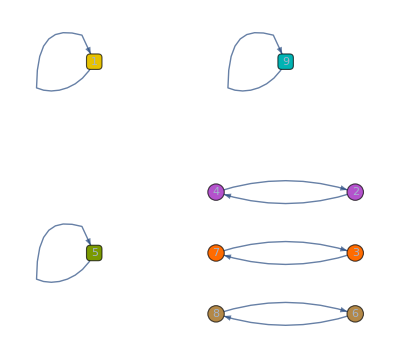

```mathematica
Graph[proc1]
```

Możemy teraz łatwo zadawać różne pytania związane z samych procesem. W pierwszej kolejności możemy generować ściezki. Poniżej jest kilka takich ścieżek razem z wizualizacją.

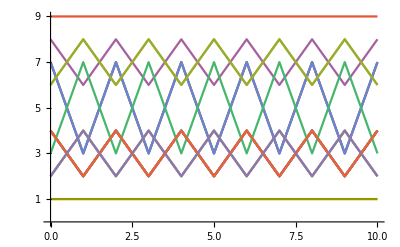

```mathematica
ListPlot[RandomFunction[proc1,{0,10},20],Joined->True,Ticks->{Automatic,Range[9]}]
```

Generalnie możemy zadać pytanie o wiele własności takiego procesu, który ma oczywiście przełożenie na zachowanie się procesu uczenia.

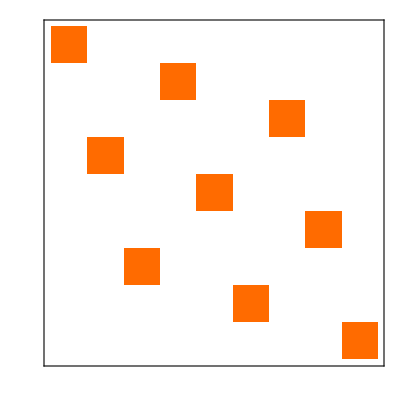
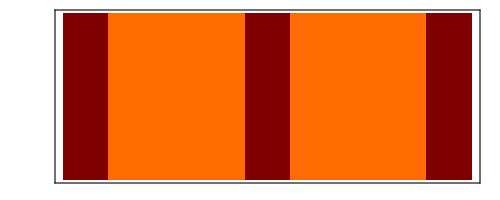
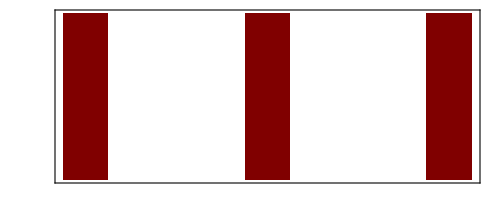
Basic Properties | 
TransitionMatrix | -Graphics-
HoldingTimeMean | -Graphics-
HoldingTimeVariance | -Graphics-
Structural Properties | 
CommunicatingClasses | {1}, {2,4}, {3,7}, {5}, {6,8}, {9}
RecurrentClasses | {1}, {2,4}, {3,7}, {5}, {6,8}, {9}
TransientClasses | None
AbsorbingClasses | {1}, {5}, {9}
PeriodicClasses | {2,4}, {3,7}, {6,8}
Periods | {2,2,2}
Irreducible | False
Aperiodic | False
Primitive | False
Limiting Properties | 
LimitTransitionMatrix | -Graphics-
Reversible | False

```mathematica
MarkovProcessProperties[proc1]
```

Warto zauważyć, że stany pochłaniające to równowagi Nasha w strategiach czystych. Zobaczmy jak zachowuje się taki sam łańcuch ale dla zaburzonej najlepszej odpowiedzi. Warto zauważyć, że ponieważ prawdopodobieństwo losowego woboru jest niezależne pomiędzy graczami oraz pomiędzy okresami więc prawdopodobieństwo błędnego przejścia pomiędzy dowolnymi stanami wynosi 1/9 a więc mamy następującą macierz przejścia.

```mathematica
trans2=(1-ϵ) trans + ϵ Table[1/9,{j,1,9},{k,1,9}];
MatrixForm[trans2]
```

(1-(8 ϵ)/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9
ϵ/9 | ϵ/9 | ϵ/9 | 1-(8 ϵ)/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9
ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | 1-(8 ϵ)/9 | ϵ/9 | ϵ/9
ϵ/9 | 1-(8 ϵ)/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9
ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | 1-(8 ϵ)/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9
ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | 1-(8 ϵ)/9 | ϵ/9
ϵ/9 | ϵ/9 | 1-(8 ϵ)/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9
ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | 1-(8 ϵ)/9 | ϵ/9 | ϵ/9 | ϵ/9
ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | ϵ/9 | 1-(8 ϵ)/9)

```mathematica
proc2=DiscreteMarkovProcess[ini,trans2];
```

Mając tak zdefiniowany proces możemy przyjąć jakąś wartość numeryczną dla ϵ.

```mathematica
proc2a=proc2/.ϵ->1/100;
```

Tak zdefiniowany proces nie ma stanów pochłaniających co można zobaczyć na poniższym grafie.

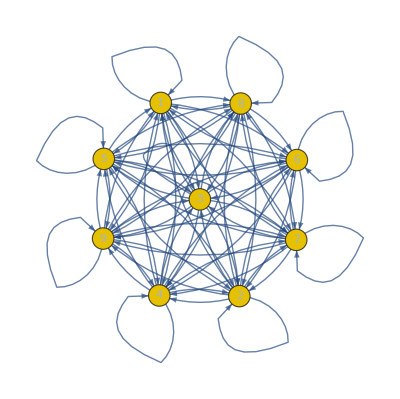

```mathematica
Graph[proc2a]
```

Możemy też sprawdzić podstawowe własności łańcucha.

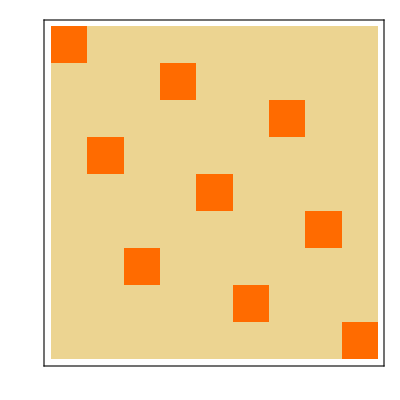
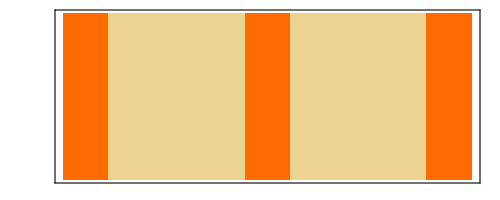
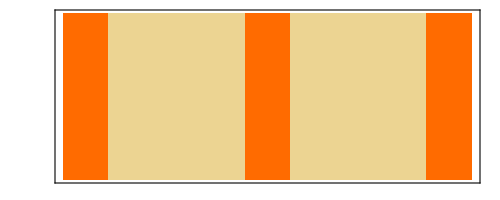
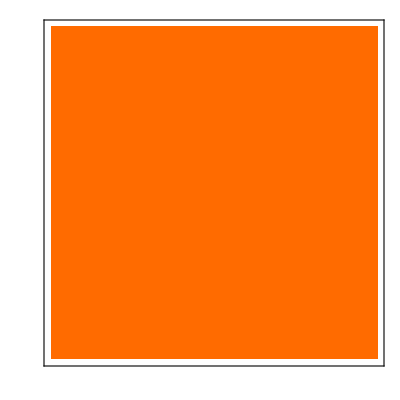
Basic Properties | 
TransitionMatrix | -Graphics-
HoldingTimeMean | -Graphics-
HoldingTimeVariance | -Graphics-
Structural Properties | 
CommunicatingClasses | {1,…,9}
RecurrentClasses | {1,…,9}
TransientClasses | None
AbsorbingClasses | None
PeriodicClasses | None
Periods | {}
Irreducible | True
Aperiodic | True
Primitive | True
Limiting Properties | 
LimitTransitionMatrix | -Graphics-
Reversible | True

```mathematica
MarkovProcessProperties[proc2a]
```

Typowe zachowanie takiego łańcucha jest pokazane poniżej. Warto zauważyć, że dodanie losowości do wyboru daje nam jedynie przechodzenie pomiędzy klasami komunikującymi się w niezaburzonym łańcuch Markowa.

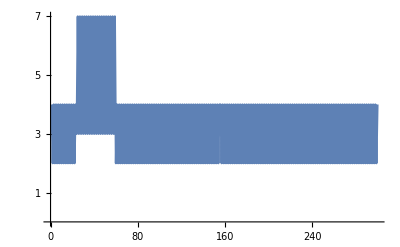

```mathematica
ListPlot[
RandomFunction[proc2a,{1,300}],
Ticks->{Automatic,Range[9]},
Joined->True
]
```

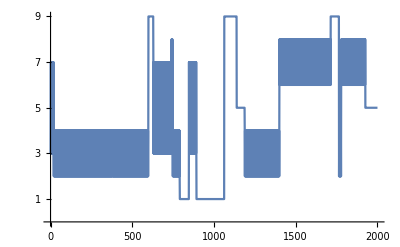

```mathematica
ListPlot[
RandomFunction[proc2a,{1,2000}],
Ticks->{Automatic,Range[9]},
Joined->True
]
```

Oczywiście możemy zadawać pytania dotyczące różnych prawdopodobieństw. Przykładowo, jakie jest prawdopodobieństwo, że w chwili t łańcuch będzie w danym stanie.

```mathematica
Probability[x[t]==2,x\[Distributed]proc2]
```

1/9

Dzieje się tak dlatego, że zdefiniowany powyżej łańcuch jest stacjonarny (silnie) bo rozkład początkowy jest również rozkładem stacjonarnym.

```mathematica
StationaryDistribution[proc2a]
```

DiscreteUniformDistribution[{1,9}]

Uwaga. Całość powyższej analizy można zapakować do jednej głównej funkcji, która z gry tworzy odpowiedni łańcuch Markowa. Poniżej jest takie rozwiązanie. Warto jednak zwrócić uwagę, że należy zadbać o to aby odpowiednio wstawiać prawdopodobieństwa przejścia w przypadku gdy jest więcej niż jednak najlepsza odpowiedź. Poniżej przyjęto założenie, że prawdopodobieństwa przejścia są w takim przykładzie rozłożone równo.

```mathematica
(* czysto techniczna funkcja *)
ClearAll[tech1]
tech1[qq_]:=Module[{q,dim,ret,k},
q=Last[qq];
dim=Length[q];
ret=q/.Point->List/.Simplex->Sequence;
ret=Sequence@@ret;
ret=Flatten[Outer[List,ret,1],dim-1];
Table[{First[qq],ret⟦k⟧},{k,1,Length[ret]}]
]
```

```mathematica
ClearAll[discreteMarkoProcessFromGame]
discreteMarkoProcessFromGame[g_,ϵ_,ini_]:=Module[{k,dim,numOfStates,profiles,states,tostates,trans,transtest,w,pos},
dim=Dimensions[g["player 1"]];
numOfStates=dim/.List->Times;
(* stworzenie słowników *)
profiles=Sequence@@Table[IdentityMatrix[dim⟦k⟧],{k,1,Length[dim]}];
states=<|Thread[Range[numOfStates]->Flatten[Outer[List, profiles,1],Length[g]-1]]|>;
tostates=Thread[Flatten[Outer[List, profiles,1],Length[g]-1]->Range[numOfStates]];
(* macierz przejścia *)
transtest=Table[
{k,bestReply[g,states[k]]},
{k,1,numOfStates}
];
transtest=tech1/@transtest;
transtest=transtest/.tostates;
transtest=Cases[transtest,{_?IntegerQ,_?IntegerQ},Infinity];
w=ConstantArray[0,Length[transtest]];
Table[
pos=Flatten@Position[transtest,{k,_}];
w⟦pos⟧=1/Length[pos],
{k,1,numOfStates}];
trans=Thread[transtest->w];
trans=SparseArray[trans,{numOfStates,numOfStates}];
(* nakładanie szumu *)
trans=(1-ϵ) trans + ϵ ConstantArray[1/numOfStates,{numOfStates,numOfStates}];
(* zwracanie *)
<|
"process"->DiscreteMarkovProcess[ini,trans],
"translation"->states
|>
]
```

Mając powyższa funkcję możemy popatrzeń na kilka prostych grier ale również na kilka większych. Pamiętamy, że wszystkie punkty pochłaniające w łańcuchu bez szumu są ścisłymi równowagami Nasha (stric Nash equilibrium). Dla wygody zdefiniujemy jeszcze prostą funkcję do “ładnego” rysowania grafów odpowiadających łańcuchom Markowa.

```mathematica
ClearAll[plotMarkovGraph]
plotMarkovGraph[q_,eps_:.1]:=Module[{wm,mw,el},
wm=MarkovProcessProperties[q,"TransitionMatrix"];
mw=(#->Opacity[Max[eps,wm⟦#/.DirectedEdge->Sequence⟧]])&;
el=EdgeList[Graph[q]];
Graph[q,EdgeStyle->(mw/@el)]
]
```

Przykład. Definiujemy bardzo prostą grę.

```mathematica
g1=<|"player 1"->{{1,0},{0,1}},"player 2"->{{1,0},{0,1}}|>;
MatrixForm/@g1
```

<|player 1→(1 | 0
0 | 1),player 2→(1 | 0
0 | 1)|>

Definiujemy odpowiadający łańcuch Markowa.

```mathematica
proc1=discreteMarkoProcessFromGame[g1,0,{1,1,1,1}/4];
proc1noise=discreteMarkoProcessFromGame[g1,1/5,{1,1,1,1}/4];
```

Odpowiadające grafy dla łańcucha bez i z szumem.

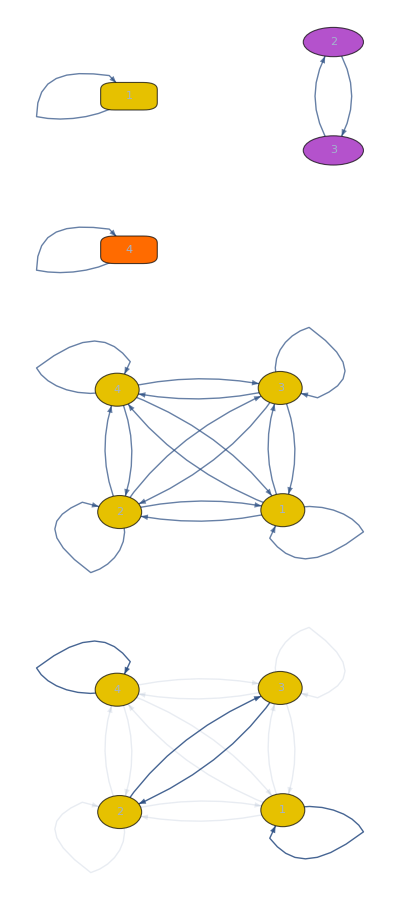

```mathematica
Grid[{
{Graph[proc1["process"]]},
{Graph[proc1noise["process"]]},
{plotMarkovGraph[proc1noise["process"]]}
},Frame->All]
```

```mathematica
MarkovProcessProperties[proc1["process"],"AbsorbingClasses"]
```

{{1},{4}}

```mathematica
{2,3}/.proc1["translation"]//Column
```

{{1,0},{0,1}}
{{0,1},{1,0}}

Przykład. Rozpatrzmy poprzednią grę RSP.

```mathematica
g2=<|"player 1"->NestList[RotateRight,{1,0,2},2],"player 2"->Transpose[NestList[RotateRight,{1,0,2},2]]|>;
MatrixForm/@g2
```

<|player 1→(1 | 0 | 2
2 | 1 | 0
0 | 2 | 1),player 2→(1 | 2 | 0
0 | 1 | 2
2 | 0 | 1)|>

Podobnie jak powyżej definiujemy dwa łańcuch Markowa.

```mathematica
proc2=discreteMarkoProcessFromGame[g2,0,ConstantArray[1,9]/9];
proc2noise=discreteMarkoProcessFromGame[g2,1/10,ConstantArray[1,9]/9];
```

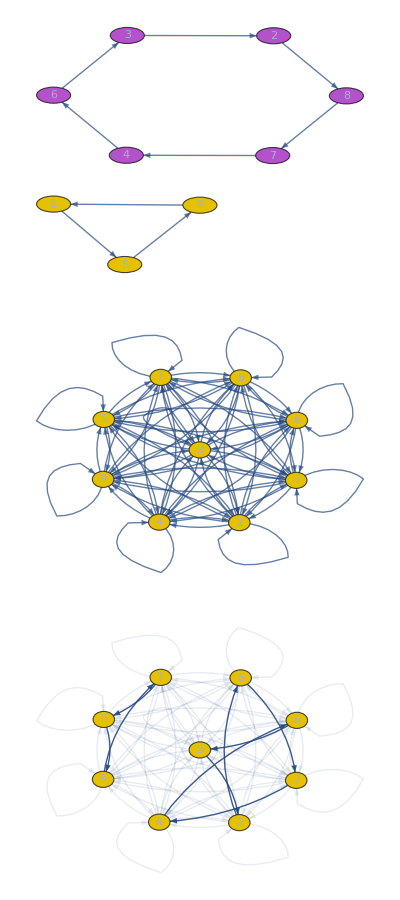

```mathematica
Grid[{
{Graph[proc2["process"]]},
{Graph[proc2noise["process"]]},
{plotMarkovGraph[proc2noise["process"]]}
},Frame->All]
```

W powyższym przykładzie widzimy, że nie ma żadnej równowagi w strategiach czystych. Możemy zobaczyć jakie profile odpowiadają mniejszemu cyklowi.

```mathematica
{1,5,9}/.proc2["translation"]
```

{{{1,0,0},{1,0,0}},{{0,1,0},{0,1,0}},{{0,0,1},{0,0,1}}}

Jak widać jest to cykl odpowiadający symetrycznym profilom strategii czystych.  Możemy również zobaczyć jak wyglądają profile na dłuższym cyklu.

```mathematica
Last@MarkovProcessProperties[proc2["process"],"CommunicatingClasses"]/.proc2["translation"]//Column
```

{{1,0,0},{0,1,0}}
{{1,0,0},{0,0,1}}
{{0,1,0},{1,0,0}}
{{0,1,0},{0,0,1}}
{{0,0,1},{1,0,0}}
{{0,0,1},{0,1,0}}

Przykład. W przypadku większych gier, struktura gry jest zazwyczaj znacznie ciekawsza. Definiujemy losową grę dla trzech graczy.

```mathematica
g3=generateRandomGame[BinomialDistribution[30,1/10],{2,3,4}];
MatrixForm/@g3
```

<|player 1→((5
5
4
3) | (2
0
3
3) | (3
4
3
5)
(2
3
2
5) | (1
3
1
3) | (4
2
0
4)),player 2→((5
3
3
2) | (4
5
5
1) | (1
1
2
5)
(3
2
2
3) | (2
3
0
2) | (5
2
1
4)),player 3→((4
5
2
4) | (1
6
3
2) | (4
2
3
3)
(3
2
3
2) | (4
5
3
4) | (3
2
4
4))|>

Podobnie jak poprzednio definiujemy dwa łańcuch Markowa. Łańcuch bez szumu wygląda w następujacy sposób.

```mathematica
proc3=discreteMarkoProcessFromGame[g3,0,ConstantArray[1,2 3 4]/(2 3 4)];
```

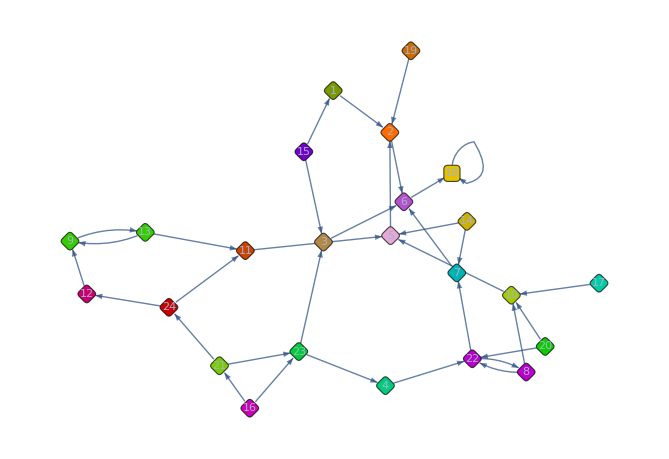

```mathematica
Graph[proc3["process"]]
```

Możemy teraz znaleźć szybko ścisłe równowagi Nasha.

```mathematica
Flatten@MarkovProcessProperties[proc3["process"],"AbsorbingClasses"]
```

{18}

```mathematica
Flatten@MarkovProcessProperties[proc3["process"],"AbsorbingClasses"]/.proc3["translation"]
```

{{{0,1},{0,1,0},{0,1,0,0}}}

Możemy również popatrzeć na klasy stanów, które są recurrent (powtarzalne?). To będzie ten zbiór profili, który będzie zawierał nośniki wszystkich równowag Nasha. Możemy odpowiednio zaznaczyć je w ramach grafu. Stany z tych klas są najistotniejsze w grze.

```mathematica
MarkovProcessProperties[proc3["process"],"RecurrentClasses"]
```

{{18}}

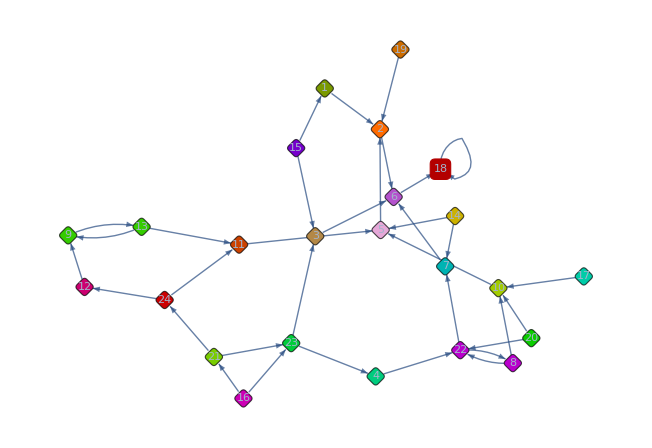

```mathematica
HighlightGraph[
Graph[proc3["process"]], 
MarkovProcessProperties[proc3["process"],"RecurrentClasses"],
VertexSize->.7]
```

Klasy stanów transient są mało istotne, proces nawet jeżeli zacznie z takiego stanu to ostatecznie opuści go i nigdy do niego nie wróci co automatycznie pokazuje, że taki profil nie może znajdować się w nośniku żadnej równowagi Nasha.

```mathematica
MarkovProcessProperties[proc3["process"],"TransientClasses"]
```

{{6},{2},{1},{3},{7},{5},{10},{8,22},{4},{11},{9,13},{12},{14},{15},{23},{24},{21},{16},{17},{19},{20}}

Proces z szumem nie ma specjalnie ciekawego grafu ale za to ma znacznie ciekawsze informacje związane z miarą stacjonarną.

```mathematica
proc3noise=discreteMarkoProcessFromGame[g3,1/10,ConstantArray[1,2 3 4]/(2 3 4)];
```

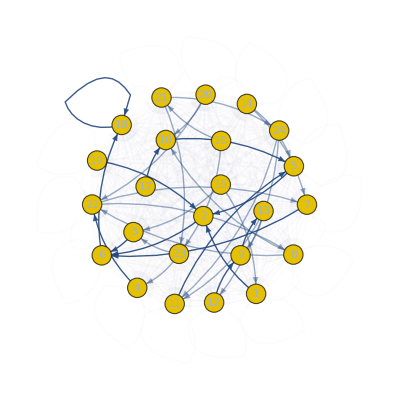

```mathematica
plotMarkovGraph[proc3noise["process"],0.01]
```

Poniżej jeszcze raz ten sam graf ale z zaznaczonymi stanami recurrent.

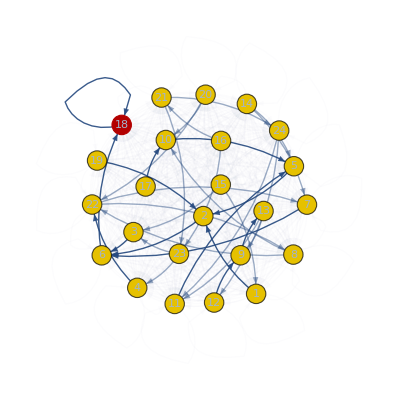

```mathematica
HighlightGraph[
plotMarkovGraph[proc3noise["process"],0.01],
MarkovProcessProperties[proc3["process"],"RecurrentClasses"]
]
```

Rozkład stacjonarny jest łatwy do policzenia.

```mathematica
𝒟=StationaryDistribution[proc3noise["process"]];
```

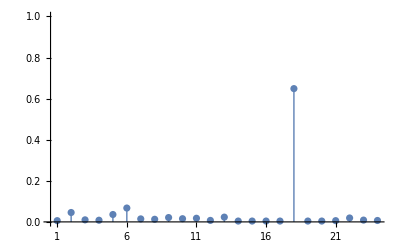

```mathematica
ListPlot[
Table[PDF[𝒟,k],{k,1,24}],
Filling->Axis,
PlotRange->{All, {0,1}},
Ticks->{Range[24],Automatic},
FillingStyle->Directive[Thick]
]
```